## Recursion equation for Random Walk expected passage time (Section 4.3)

Consider the expected passage time for the Random Walk on {0,1,...,M} to the absorbing states {0,M}. We can solve for it using Theorem 4.1. What is the behavior when M grows?

### Assume first that q is not 1/2. The Recursion Equation is inhomogeneous, and its solution has the form:

```mathematica
RSolveValue[{q*f[x+1]-f[x]+(1-q)*f[x-1]==-1,f[0]==0,f[M]==0},f[x],x]
```

-1/((-1+((1-q)/q)^M) (-1+2 q)^2)(-1+1/q)^(-M-x) (-M (-1+1/q)^(M+x)+M (-1+1/q)^(M+x) ((1-q)/q)^x+2 M (-1+1/q)^(M+x) q-(-1+1/q)^x ((1-q)/q)^M q+(-1+1/q)^(M+x) ((1-q)/q)^M q+(-1+1/q)^M ((1-q)/q)^x q-(-1+1/q)^(M+x) ((1-q)/q)^x q-2 M (-1+1/q)^(M+x) ((1-q)/q)^x q-(-1+1/q)^M ((1-q)/q)^(M+x) q+(-1+1/q)^x ((1-q)/q)^(M+x) q+(-1+1/q)^(M+x) x-(-1+1/q)^(M+x) ((1-q)/q)^M x-2 (-1+1/q)^(M+x) q x+2 (-1+1/q)^(M+x) ((1-q)/q)^M q x)

```mathematica
FullSimplify[%]
```

(M (-1+(-1+1/q)^x)+x-(-1+1/q)^M x)/((-1+(-1+1/q)^M) (-1+2 q))

### Let' s plot with the value x = 1:

```mathematica
F[M_,q_]:=((M (-1+(-1+1/q)^x)+x-(-1+1/q)^M x)/((-1+(-1+1/q)^M) (-1+2 q)))/.{x->1};
```

Plotting for some q' s less than 1/2:

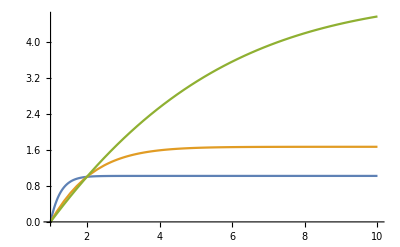

```mathematica
Plot[{F[M,.01],F[M,.2],F[M,.4]},{M,1,10}]
```

Plotting for some q' s greater than 1/2:

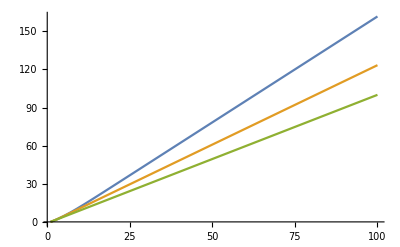

```mathematica
Plot[{F[M,.6],F[M,.8],F[M,.99]},{M,1,100}]
```

Example limits:

```mathematica
Limit[F[M,.1],M->Infinity]
Limit[F[M,.45],M->Infinity]
Limit[F[M,.55],M->Infinity]
Limit[F[M,.9],M->Infinity]
```

1.25

10.

∞

∞

### We see that the limit (as M grows) exists if q < 1/2 and is infinite if q > 1/2.

### Assume then that q = 1/2. The Recursion Equation is inhomogeneous, and its solution has the form:

```mathematica
RSolveValue[{(1/2)*f[x+1]-f[x]+(1-(1/2))*f[x-1]==-1,f[0]==0,f[M]==0},f[x],x]
```

M x-x^2

### Let' s plot with the value x = 1:

```mathematica
G[M_]:=(M x-x^2)/.{x->1};
```

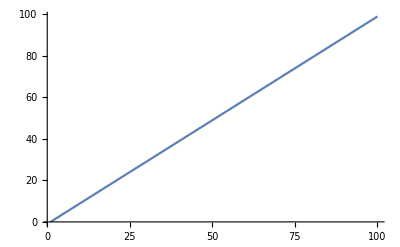

```mathematica
Plot[G[M],{M,1,100}]
```

### We see that the limit (as M grows) is infinite also if q = 1/2.